CITE THIS NOTEBOOK: Framework for liquid crystal based particle models by Jarek Duda. Wolfram Community MAR 20 2023.
ORIGINAL ARTICLE:  Jarek Duda, https://arxiv.org/pdf/2108.07896 
NOTEBOOKS: https://github.com/JarekDuda/liquid-crystals-particle-models/

Article Abstract: Liquid crystals, widely used e.g. in LCD, allow for topologically nontrivial structures e.g. hedgehog-like. For such quantized topological charges there were experimentally observed long-range e.g. Coulomb-like interactions ([1],[2],[3],[4]), suggesting exploration of boundaries of its resemblance with with particle physics . This article discusses modification of popular Landau-de Gennes model (awarded by Nobel prize) for Lorentz invariant Lagrangian to recreate electromagnetism for such topological charges. Interpreting field curvature as dual electromagnetic F tensor, Gauss law counts topological charge - getting charge quantization. Higgs-like potential allows to regularize charge to finite energy. Further topological excitations resemble 3 leptons, baryons with proton lighter than neutron, nuclei and other particles.

Topological defects in liquid crystals have particle-like behavior for quantized topological charges (e.g. [1],[2],[3],[4]), suggesting exploration of boundaries of such similarity with particle physics. This article contains brief popular introduction to  such approach modifying Landau-de Gennes model, its further elaboration can be found in arXiv:2108.07896, and available notebooks, video lecture.
	Electromagnetism has two basic issues: lack of charge quantization (that Gauss law returns charge as a real number), and infinite energy of electric field of a charge. Manfried Faber has suggested a simple way to repair both [5], [6]: consider field of unitary vectors ,  define its curvature as dual electromagnetic F tensor (with switched E and B) - this way Gauss law counts topological charge, enforcing its quantization. Using Higgs-like potential e.g.  gives tendency for unitary vectors ( case referred as vacuum), still allowing to deform the center of singularity to a finite energy:

-Graphics-

	To calculate 2D topological charge above, also called winding number, perform a loop around - counting rotation of the field. Naively it is an integer multiplicity of full rotations, e.g. +1 topological charge for the hedgehog configuration above. However, analogously calculating for the configuration on the right above, we get -1/2 full rotations. It is thanks to symmetry of used ellipses: that rotating it by 180 degrees, it is already the same ellipse. This kind of 2D topological charges are common as cross-sections of vortices e.g. in superconductors or superfluids - carrying quants of magnetic field or angular momentum ( https://en.wikipedia.org/wiki/Macroscopic_quantum_phenomena ) due to such topological quantization. Possibility of 1/2 topological charges here, related with magnetic field and angular momentum, suggests to interpret such 2D topological charge as spin. Additional argument for this spin resemblance is offered by quantum rotation operator - saying that rotating spin  particle by  angle, rotates quantum phase by  - exactly as for the above 2D topological charges.
	While 2D topological charge (e.g. in cross-section of vortex) resembles spin, in 3D there are also point-like 3D topological charges resembling electric charges, e.g. hedgehog. We can analogously calculate this 3D topological charge by integration using Gauss-Bonnet theorem - of curvature on a closed surface. Hence interpreting this curvature as electric field, Gauss law counts topological charge - getting built-in charge quantization. For example in liquid crystals there are observed long-range interactions for such topological charges: [1],[2],[3],[4].

-Graphics-

	While the mentioned experiments mainly use uniaxial nematic liquid crystals (assuming molecules of cylindrical symmetry), a natural generalization is to biaxial nematic without such symmetry - modeled as ellipsoids of 3 different axes. As in the figure above, for biaxial nematic we can build hedgehog configuration with one of 3 axes - getting three objects of the same electric charge, but of different energy (mass) - resembling 3 leptons. Additionally, forming hedgehog of one axis, then trying to align the second axis on sphere, the hairy ball theorem says it cannot be done - there is a topological conflict requiring additional vortex-like singularites: here suggesting why leptons require to also have spin.
	Such hedgehog still has freedom for evolution of internal rotation, which resembles Berry/quantum phase rotation in so called de Broglie clock/zitterbewegung, confirmed experimentally for electron [7]. Below is a short code drawing such hedgehogs for various phase , its larger demonstration version is available in https://demonstrations.wolfram.com/TopologicalChargesInBiaxialNematicLiquidCrystal/

```mathematica
𝔇={0.1,0.01,0.001}; (* eigenvalues as shape of molecule *)
Gx={{0,0,0},{0,0,-1},{0,1,0}};Gy={{0,0,1},{0,0,0},{-1,0,0}};Gz={{0,-1,0},{1,0,0},{0,0,0}};  (* generators *)
Q=Simplify[MatrixExp[ϕ*Gz].MatrixExp[θ*Gy].MatrixExp[ψ*Gx]/.{ϕ->ArcTan[x,y],θ->-ArcTan[Sqrt[x^2+y^2],z]}]; (* hedgehog *)
M=Simplify[Q.DiagonalMatrix[𝔇].Transpose[Q]];pts=SpherePoints[300];
Row[Table[Graphics3D[{Table[Ellipsoid[p,M/.{x->p[[1]],y->p[[2]],z->p[[3]]}],{p,pts}],Gray,Sphere[{0,0,0},1]},Boxed->False],{ψ,0,Pi,Pi/9}]]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

Mathematically biaxial nematics liquid crystals are often modelled with Landau-de Gennes model [8] by Nobel prize winner Pierre-Gilles de Gennes. As in the above code, it uses field of real symmetric 3x3 matrices, here referred as , with eigenvalues defining shape , and corresponding eigenvalues being directions of axes. We need Higgs-like potential to have tendency for some preferred shape, still allowing to deform it e.g. to prevent infinite energy in singularities like the center of hedgehog. While there are many ways to choose such potential, for simplicity imagine it is  for  being some fixed preferred shape - model parameters. 
	Let us now focus on vacuum dynamics: of SO(3) rotations for . In the original Landau-de Gennes model behavior is defined by free energy, lacking time derivative hence time evolution is unclear. In contrast, particle model should use Lorentz invariant Lagrangian formalism, recreating electromagnetism for topological charges. As mentioned, to make Gauss law count topological charge, we interpret field curvature as electromagnetic dual F tensor ( with replaced electric and magnetic fields), then use standard  term as in electromagnetic Lagrangian. In the original Faber’s model ([5], [6]) such curvature of field of unitary vectors  as in uniaxial nematic is defined as:
 curvature,  where  is affine connection.
	For a few reasons we would like to generalize it to biaxial nematic with  (for ) field, especially the SO(3) rotation dynamics. Affine connection can be defined as  , which is a real antisymmetric matrix defining local rotation: in 3D having 3 coordinates (6 in 4D with addition of boosts, SO(3) -> SO(1,3) vacuum) which can be interpreted as vector as previously. To get curvature analogue directly from  field, commutator  seems a natural tool - which for rotations (fixed shape =0) turns out to be built of curvatures weighted by shape:

```mathematica
sub=Flatten[Table[Cross[{Subscript[Γ, μ]^1,Subscript[Γ, μ]^2,Subscript[Γ, μ]^3},{Subscript[Γ, ν]^1,Subscript[Γ, ν]^2,Subscript[Γ, ν]^3}][[i]]==Subscript[R, {μ,ν}]^i,{i,3}]];  (* curvatures *)
com[A_,B_]:=A.B-B.A; Subscript[Γ, μ]={{0,-Subscript[Γ, μ]^3,Subscript[Γ, μ]^2},{Subscript[Γ, μ]^3,0,-Subscript[Γ, μ]^1},{-Subscript[Γ, μ]^2,Subscript[Γ, μ]^1,0}};  
𝔇=DiagonalMatrix[{1,δ,0}];   (* assumed shape: vacuum eigenvalues 1 >> δ > 0 *)
(* O^T[Subscript[M, μ],Subscript[M, ν]]O = *)   MatrixForm[FullSimplify[com[com[Subscript[Γ, μ],𝔇],com[Subscript[Γ, μ]/.μ->ν,𝔇]],sub]]
```

(0 | δ R_{μ,ν}^3 | -((-1+δ) δ R_{μ,ν}^2)
-δ R_{μ,ν}^3 | 0 | (1-δ) R_{μ,ν}^1
(-1+δ) δ R_{μ,ν}^2 | (-1+δ) R_{μ,ν}^1 | 0)

Assuming prolate ellipsoids with 1 >> δ > 0 radii (with  related to Planck constant) - there is one long axis, and two slightly different short axes. Let us refer to dynamics of direction of the long axis as tilts, and to its internal rotation as twists (corresponding to quantum phase, governed by ~Klein-Gordon equation). We see  above has much larger contribution (tilt-tilt dynamics), which will correspond to electromagnetism. There are also lower energetic  (tilt-twist dynamics),  corresponding to quantum effects. Finally the Lagrangian should unify both EM+QM, as e.g. in QED.

-Graphics-

	Finally the discussed SO(3) vacuum can be imagined as extended phase: unifying  Berry/quantum phase, and : hypothetical more fundamental than electromagnetic  field, which topological charge is calculated by Gauss-Bonnet theorem, enforcing charge quantization. For example in  quantum momentum operator, this way both  and  contain derivatives of such extended phase:
		
-Graphics-

	Electromagnetic Hamiltonian (energy density) is sum of squares of .  Using   discussed interpretation,  is a matrix - a natural generalization of corresponding Hamiltonian is sum of squares of its coordinates (Frobenius norm). Let us check Coulomb interaction: energy of field configuration of two (here opposite) charges should  has  distance  dependence. Below is such calculation for approximated field configurations found by Manfried Faber e.g.  [6]. This article also contains more proper calculation: finding minimizing energy field configurations for given topological constraints, and comparison with this approximation. Additionally, the below calculation uses cutoff in the center of charges to remove infinite energy, while [6] does it properly - deforms the field there by including the Higgs-like potential. It leads to deformation of Coulomb interaction in femtometer-scale distance, as shown in [6] being in agreement with the running coupling effect.

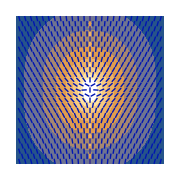
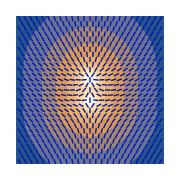
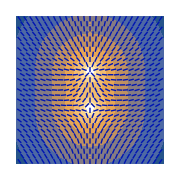
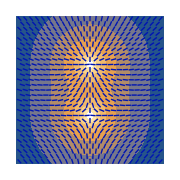
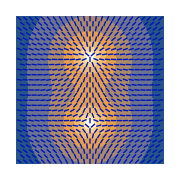

```mathematica
cos=1+(z-d)/Sqrt[(z-d)^2+r^2]-(z+d)/Sqrt[(z+d)^2+r^2];              (* Manfried Faber dipole ansatz arXiv:2210.13374 *)
n={Sqrt[1-cos^2]x/r,Sqrt[1-cos^2]y/r,cos}/.r->Sqrt[x^2+y^2];                          (* vector field *)
M=KroneckerProduct[n,n];dM={D[M,x],D[M,y],D[M,z]};com[A_,B_]:=A.B-B.A;   (* ->matrix field*)
H=Simplify[Sum[Total[com[dM[[i]],dM[[j]]]^2,2],{i,2},{j,i+1,3}]];                         (* Hamilitonian - energy density *)
Row[Table[Show[ContourPlot[Log[H]/.{y->0},{x,-2,2},{z,-2,2},Frame->False,ImageSize->Small,ContourLines->False],         (* draw field and its energy density *)
VectorPlot[n[[{1,3}]]/.y->0,{x,-2,2},{z,-2,2},VectorMarkers-> "Segment",VectorPoints->Fine]],{d,0.1,1,0.2}]]
```

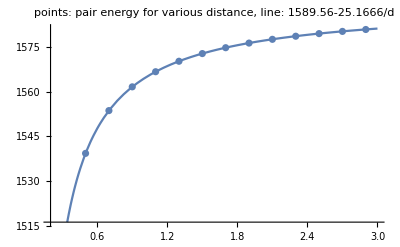

```mathematica
(* calculate total energy in various distances by integrating energy density H and compare with Coulomb potential  *)
enpm=Table[{d,Quiet[NIntegrate[4Pi*x(H/.{y->0})*Boole[x^2+(z-d)^2>0.001],   (* 0.001  cutoff *)
{x,0,Infinity},{z,0,Infinity}]]},{d,0.1,3,0.2}];                                         (* effective potential *)
ftpm=Fit[enpm,{1,1/d},d];                                                                                                               (* fit Coulomb potential *)
Show[Plot[ftpm,{d,0.2,3},PlotLabel->Row[{"points: pair energy for various distance, line: ",ftpm}]],ListPlot[enpm]]
```

To choose the final candidate for Lagrangian, Lorentz invariance suggests going to field of 4x4 real symmetric matrices , like e.g. stress-energy tensor in the general relativity. The nonstandard part is Higgs-like potential preferring some fixed set of eigenvalues, let us denote them as   with    containing additional eigenvalue . Its corresponding eigenvector: additional 0th axis can be imagined as local time direction. In constant direction of time axis approximation, the model reduces to the previous 3D case. Allowing for  small perturbations of this time axis, leads to second set of Maxwell equations - as in gravitoelectromagnetism (GEM) approximation of the general relativity theory, confirmed by Gravity Probe B. The V=0 vacuum extends from SO(3) spatial rotations, to SO(1,3) Lorentz group - additionally including boosts.
	We can now propose Lagrangian using the  discussed generalization of curvature. For Lorentz invariance this commutator requires including spacetime signature , using . For such generalization of electromagnetic  tensor (+ quantum/Berry phase + GEM), we can use for example the Lagrangian candidate below.
	
	-Graphics-

	Such looking simple Lagrangian has surprisingly complex  behavior. Below is calculation of approximated  generalization of electromagnetic  tensor - it contains  curvature corresponding to electromagnetism, but also  curvatures corresponding  to quantum phase, and  curvatures corresponding to gravitoelectromagnetism (GEM). All of them interact in such candidate of Lagrangian, e.g. EM-GEM to bend photon trajectories near Sun, with additional complication of Higgs-like potential  activated near particles to prevent infinite energy: .

```mathematica
sub=Flatten[Table[{Cross[{Subscript[Γ, μ]^1,Subscript[Γ, μ]^2,Subscript[Γ, μ]^3},{Subscript[Γ, ν]^1,Subscript[Γ, ν]^2,Subscript[Γ, ν]^3}][[i]]==Subscript[R, {μ,ν}]^i,Cross[{Subscript[Γ̃, μ]^1,Subscript[Γ̃, μ]^2,Subscript[Γ̃, μ]^3},{Subscript[Γ̃, ν]^1,Subscript[Γ̃, ν]^2,Subscript[Γ̃, ν]^3}][[i]]==Subscript[R̃, {μ,ν}]^i},{i,3}]]; 
Subscript[Γ, μ]={{0,Subscript[Γ̃, μ]^1,Subscript[Γ̃, μ]^2,Subscript[Γ̃, μ]^3},{Subscript[Γ̃, μ]^1,0,-Subscript[Γ, μ]^3,Subscript[Γ, μ]^2},{Subscript[Γ̃, μ]^2,Subscript[Γ, μ]^3,0,-Subscript[Γ, μ]^1},{Subscript[Γ̃, μ]^3,-Subscript[Γ, μ]^2,Subscript[Γ, μ]^1,0}};                (*3D rotations + boosts *)
ξ=DiagonalMatrix[{-1,1,1,1}];coms[A_,B_]:=A.ξ.B-B.ξ.A;𝔇=DiagonalMatrix[{g,1,δ,0}];Subscript[M̄, μ]=coms[Subscript[Γ, μ],𝔇];
Subscript[M̄, μ]={{0,g Subscript[Γ̃, μ]^1,g Subscript[Γ̃, μ]^2,g Subscript[Γ̃, μ]^3},{-g Subscript[Γ̃, μ]^1,0,Subscript[Γ, μ]^3,-Subscript[Γ, μ]^2},{-g Subscript[Γ̃, μ]^2,Subscript[Γ, μ]^3,0,δ Subscript[Γ, μ]^1},{-g Subscript[Γ̃, μ]^3,-Subscript[Γ, μ]^2,δ Subscript[Γ, μ]^1,0}}; (* g >> 1 >> δ > 0 approximation *)
Style[(Subscript[F̄, μν]=FullSimplify[coms[Subscript[M̄, μ],Subscript[M̄, μ]/.μ->ν],sub])//MatrixForm,Bold]
```

(0 | g (Γ_ν^3 (Γ̃)_μ^2-Γ_ν^2 (Γ̃)_μ^3-Γ_μ^3 (Γ̃)_ν^2+Γ_μ^2 (Γ̃)_ν^3) | g (Γ_ν^3 (Γ̃)_μ^1+δ Γ_ν^1 (Γ̃)_μ^3-Γ_μ^3 (Γ̃)_ν^1-δ Γ_μ^1 (Γ̃)_ν^3) | g (-Γ_ν^2 (Γ̃)_μ^1+δ Γ_ν^1 (Γ̃)_μ^2+Γ_μ^2 (Γ̃)_ν^1-δ Γ_μ^1 (Γ̃)_ν^2)
g (Γ_ν^3 (Γ̃)_μ^2-Γ_ν^2 (Γ̃)_μ^3-Γ_μ^3 (Γ̃)_ν^2+Γ_μ^2 (Γ̃)_ν^3) | 0 | δ R_{μ,ν}^3+g^2 (R̃)_{μ,ν}^3 | δ R_{μ,ν}^2-g^2 (R̃)_{μ,ν}^2
g (Γ_ν^3 (Γ̃)_μ^1+δ Γ_ν^1 (Γ̃)_μ^3-Γ_μ^3 (Γ̃)_ν^1-δ Γ_μ^1 (Γ̃)_ν^3) | -δ R_{μ,ν}^3-g^2 (R̃)_{μ,ν}^3 | 0 | R_{μ,ν}^1+g^2 (R̃)_{μ,ν}^1
g (-Γ_ν^2 (Γ̃)_μ^1+δ Γ_ν^1 (Γ̃)_μ^2+Γ_μ^2 (Γ̃)_ν^1-δ Γ_μ^1 (Γ̃)_ν^2) | -δ R_{μ,ν}^2+g^2 (R̃)_{μ,ν}^2 | -R_{μ,ν}^1-g^2 (R̃)_{μ,ν}^1 | 0)

The discussed simple looking Lagrangian  also suggests further topological excitations, and surprisingly, at least qualitatively, they seem to resemble further particles. For example it allows for stable vortices like fluxons, which can form knots - the simplest knots seem to resemble baryons, more complex ones resemble nuclei - knotted with fluxons binding against Coulomb repulsion, including additional halo neutrons stably bind in a few femtometer distance e.g. in helium-6, lithium-11. In baryon as the simplest knot, as in the below diagrams, the external vortex deforms the internal one as in hedgehog - this way baryon structure enforces some positive charge (can be fractional). Proton can just enclose this hedgehog, while neutron has to compensate it - explaining why neutron is heavier than proton. In deuteron two baryons share a single charge - what allows for energy savings as the binding energy, also explaining its large 0.2859 e·fm^2 electric quadrupole moment (would be 0 for proton-neutron as point charges). Strangeness is additional quantized property, which might be explained by internal twists of the vortex around.

To summarize,  the discussed simple looking model:  Lagrangian for real-symmetric tensor field , seems to allow to unify electromagnetism + quantum/Berry phased + gravitoelectromagnetism as vacuum dynamics, with topological excitations starting with resemblance of 3 leptons, baryons, nuclei. More details can be found in arXiv:2108.07896, however, many questions are still to be resolved, starting with the exact Higgs-like potential , fitting parameters for agreement with nature, and understanding mathematical consequences of such model - finally requiring numerical simulations. Hopefully, effective dynamics of such topological soliton multiple-particle model, after 2nd quantization will turn out in agreement with quantum field theory of the Standard Model - allowing to reduce its number of parameter from  to a few, also providing more intuitive understanding of field dynamics, mechanisms e.g. for charge quantization.

### References

[1]  Y. Shen and I. Dierking, “Annihilation dynamics of topological defects induced by microparticles in nematic liquid crystals,” Soft matter, vol. 15, no. 43, pp. 8749–8757, 2019, https://pubs.rsc.org/en/content/articlelanding/2019/sm/c9sm01710k

[2] P. Poulin, H. Stark, T. Lubensky, and D. Weitz, “Novel colloidal interactions in anisotropic ﬂuids,” Science, vol. 275, no. 5307, pp. 1770–1773, 1997, https://pubmed.ncbi.nlm.nih.gov/9065396/

[3] R. Ruhwandl and E. Terentjev, “Long-range forces and aggregation of colloid particles in a nematic liquid crystal,” Physical Review E, vol. 55, no. 3, p. 2958, 1997, https://journals.aps.org/pre/abstract/10.1103/PhysRevE.55.2958

[4] J. Wabnig, J. Resch, D. Theuerkauf, F. Anmasser, and M. Faber, “Numerical evaluation of a soliton pair with long range interaction,” 2022, arXiv preprint arXiv:2210.13374

[5] M.Faber, “A geometric model in 3+ 1d space-time for electrodynamic phenomena,” Universe, vol. 8, no. 2, p. 73, 2022, https://www.mdpi.com/2218-1997/8/2/73

[6] R. Ruhwandl and E. Terentjev, “Long-range forces and aggregation of colloid particles in a nematic liquid crystal,” Physical Review E, vol. 55, no. 3, p. 2958, 1997, https://journals.aps.org/pre/abstract/10.1103/PhysRevE.55.2958

[7] P. Catillon, N. Cue, M. Gaillard, R. Genre, M. Gouanere, R. Kirsch, J.-C. Poizat, J. Remillieux, L. Roussel, and M. Spighel, “A search for the de broglie particle internal clock by means of electron channeling,” Foundations of Physics, vol. 38, no. 7, pp. 659–664, 2008, https://link.springer.com/article/10.1007/s10701-008-9225-1

[8] P.-G. De Gennes and J. Prost, The physics of liquid crystals. Oxford university press, 1993, no. 83.